```mathematica
r1=1.1;
```

```mathematica
r2=2;
```

```mathematica
r3=5;
```

```mathematica
r4=10;
```

```mathematica
n=1000;
```

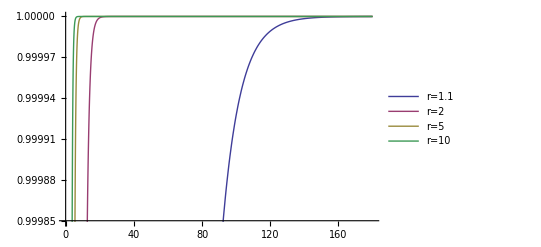

```mathematica
Plot[{(1-1/(r1^x))/(1-1/(r1^n)),(1-1/(r2^x))/(1-1/(r2^n)),(1-1/(r3^x))/(1-1/(r3^n)),(1-1/(r4^x))/(1-1/(r4^n))},{x,0,180},PlotLegends->Placed[{"r=1.1","r=2","r=5","r=10"},{0.65,0.7}]]
```

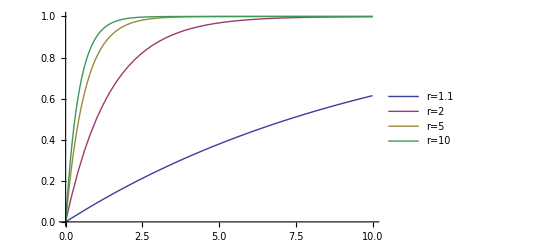

```mathematica
Plot[{(1-1/(r1^x))/(1-1/(r1^n)),(1-1/(r2^x))/(1-1/(r2^n)),(1-1/(r3^x))/(1-1/(r3^n)),(1-1/(r4^x))/(1-1/(r4^n))},{x,0,10},PlotLegends->Placed[{"r=1.1","r=2","r=5","r=10"},{0.65,0.7}]]
```

```mathematica
Manipulate[Plot[(1-1/(r^x))/(1-1/(r^n)),{x,0,10},ImageSize->800,PlotRange->{0,1}],{r,1.0001,4}]
```

```mathematica
Manipulate[Plot[(1-1/(r1^x))/(1-1/(r1^n1)),{x,0,10},ImageSize->800,PlotRange->{0,1}],{n1,100,5000}]
```

Plot::exclul: {Im[r1] - 0} must be a list of equalities or real-valued functions.

```mathematica
giver=1.4;
```

```mathematica
given=1000;
```

```mathematica
givei=1;
```

```mathematica
N[(1-1/(giver^givei))/(1-1/(giver^given))]
```

0.285714

```mathematica
(* Here I can plot the fixation probability as a function of p for a given value of n_0 *)
sgiven=1000;
```

```mathematica
sgivei=5;
```

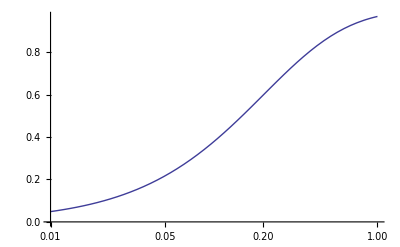

```mathematica
LogLinearPlot[(1-1/((1+sp)^sgivei))/(1-1/((1+sp)^sgiven)),{sp,0.01,1}] (* Cuz r is 1+p, hence p btw 0 and 1 *)
```

```mathematica
(* This is the computation for the approximation for the probability of killing 2 cooperators *)
```

```mathematica
M=1000;
```

```mathematica
(* This is the probability of killing exactly 2 cells in the process *)
```

```mathematica
proba=N[1-((M-2)/M)^(M-2)-Sum[(((M-2)/M)^i)*(2/M)*(((M-1)/M)^(M-3-i)),{i,0,M-3}]]
```

0.398743

```mathematica
(*Thus the probabiltiy of not killing the 2 cells is given by : Note that I might want to multiply by 999/*1000 cuz there is always the probability that I kill a cooperative group *)
1-proba
```

0.601257

```mathematica
(* Probability of killing at least 1 red cell *)
```

```mathematica
N[1-((M-2)/M)^(M-2)]
```

0.864394

```mathematica
N[Sum[(((M-2)/M)^i)*(2/M)*(((M-1)/M)^(M-3-i)),{i,0,M-3}]] (* Probability of killing exactly 1 red cell *)
```

0.465651

```mathematica
po=0.14;
```

```mathematica
p1=0.46;
```

```mathematica
fixa=Sum[po*(p1^i),{i,0,Infinity}]
```

0.259259

```mathematica
emme2=10;
```

```mathematica
partiale=Sum[po*(p1^i),{i,0,emme2-2}]+(po+p1)*p1^(emme2-2)
```

0.260223